## Goal: Reach a=1, b=1, at t=1, starting at b=0, with minimum nonadiabaticity

### Naive

(0.439983-0.789508 ⅈ | 0.145656-0.402338 ⅈ
-0.145656-0.402338 ⅈ | 0.439983+0.789508 ⅈ)

(-0.382683 | 0.92388
0.92388 | 0.382683)

Similarity of final states to final eigenstates

(0.0966156 | 0.903384
0.903384 | 0.0966156)

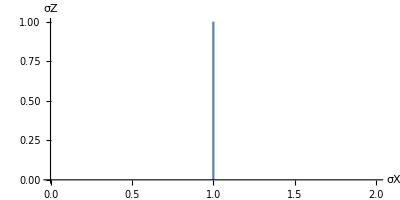

```mathematica
statusString = "";

Tmax = 1;
a = 1;
b = 1*(t/Tmax);
H = a*σZ + b*σX;

U = findEvolutionOperator[H, Tmax];
U /. t->Tmax // MatrixForm

finalEVs = Normalize /@ Eigenvectors[H /. t->Tmax] // N;
finalEVs // MatrixForm

"Similarity of final states to final eigenstates"
finalEVs.(U /. t->Tmax) // AbSq // MatrixForm

ParametricPlot[{a, b}, {t, 0, Tmax}, AxesLabel->{"σX", "σZ"}]
```

### Two-step

(0.377756+0.84099 ⅈ | -0.160807+0.352388 ⅈ
0.160807+0.352388 ⅈ | 0.377756-0.84099 ⅈ)

(0.382683 | -0.92388
-0.92388 | -0.382683)

Similarity of final states to final eigenstates

(0.0000299652 | 0.99997
0.99997 | 0.0000299652)

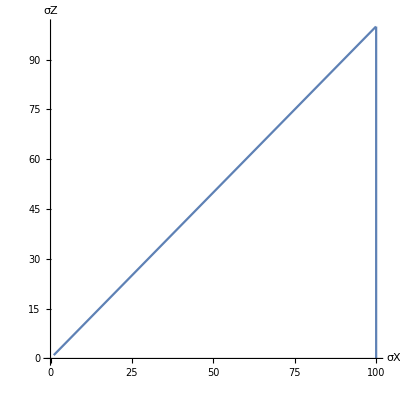

```mathematica
statusString = "";

Tmax = 1;
τ = .5;

Q = 100;
a = Piecewise[{{Q, t ≤ τ}, {Q - (Q - 1)*(t - τ)/(Tmax - τ), t > τ}}];
b = Piecewise[{{Q*t/τ, t ≤ τ}, {Q - (Q - 1)*(t - τ)/(Tmax - τ), t > τ}}];
H = a*σZ + b*σX;

U = findEvolutionOperator[H, Tmax];
U /. t->Tmax // MatrixForm

finalEVs = Normalize /@ Eigenvectors[H /. t->Tmax] // N;
finalEVs // MatrixForm

"Similarity of final states to final eigenstates"
finalEVs.(U /. t->Tmax) // AbSq // MatrixForm

ParametricPlot[{a, b}, {t, 0, Tmax}, AxesLabel->{"σX", "σZ"}]
```